## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOutRectangular.csv"],"CSV",HeaderLines->1];

αs=(Transpose@mydata)[[1]];
τs=(Transpose@mydata)[[2]];(*in IGeV*)
rs=(Transpose@mydata)[[3]];(*in IGeV*)
Dτs=(Transpose@mydata)[[4]];(*in IGeV*)
Drs=(Transpose@mydata)[[5]];(*in IGeV*)
urs=(Transpose@mydata)[[6]]; (*dimensionless*)
uτs=(Transpose@mydata)[[7]]; (*dimensionless*)
```

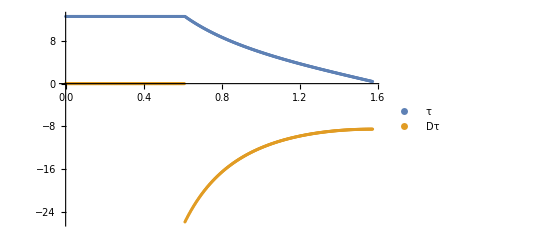

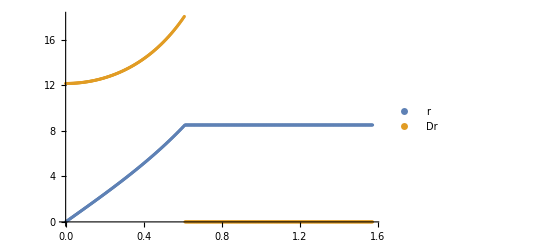

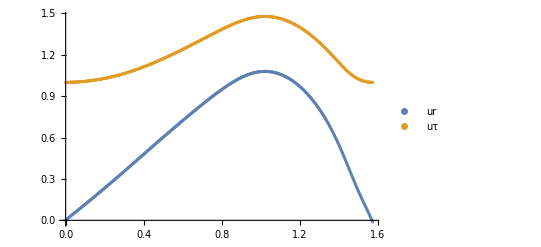

```mathematica
ListPlot[{Transpose@{αs,τs},Transpose@{αs,Dτs}},PlotLegends->{"τ","Dτ"}]
ListPlot[{Transpose@{αs,rs},Transpose@{αs,Drs}},PlotLegends->{"r","Dr"}]
ListPlot[{Transpose@{αs,urs},Transpose@{αs,uτs}},PlotLegends->{"ur","uτ"}]
```

### Define Interpolating Functions from the Data

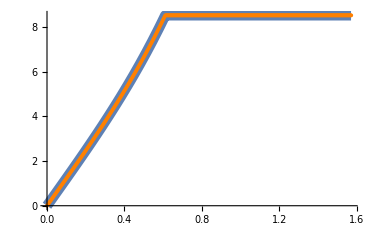

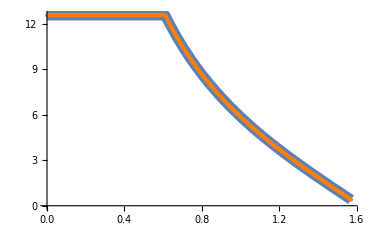

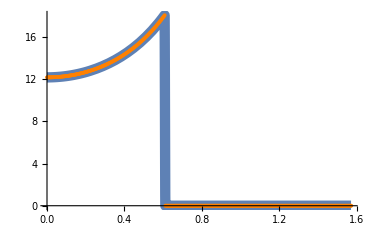

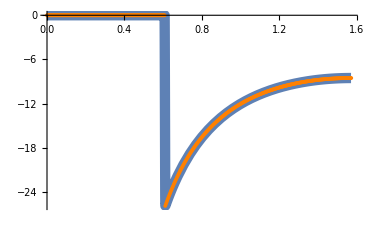

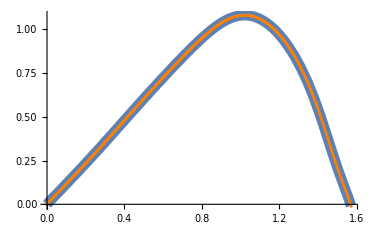

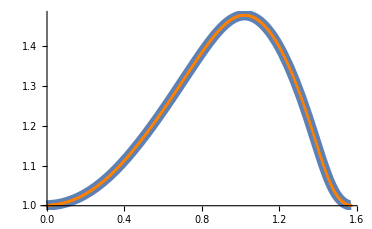

```mathematica
r=Interpolation[Transpose@{αs,rs}];
τ=Interpolation[Transpose@{αs,τs}];
Dr=Interpolation[Transpose@{αs,Drs},InterpolationOrder->1];
Dτ=Interpolation[Transpose@{αs,Dτs},InterpolationOrder->1];
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
Show[
Plot[r[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,rs},PlotStyle->{Orange}]
]
Show[
Plot[τ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,τs},PlotStyle->{Orange}]
]
Show[
Plot[Dr[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,Drs},PlotStyle->{Orange}]
]
Show[
Plot[Dτ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,Dτs},PlotStyle->{Orange}]
]
Show[
Plot[ur[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,urs},PlotStyle->{Orange}]
]
Show[
Plot[uτ[x],{x,0,Pi/2},PlotStyle->{Thickness[0.02]}],
ListPlot[Transpose@{αs,uτs},PlotStyle->{Orange}]
]
```

### Define field data from a already calculated spectrum (c++ code) in order to double check validity of code...

```mathematica
parentdir=StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/spectra_real_m140_constfield_20241029_110519/"];
allspecs=FileNames[All,parentdir];
myspec=allspecs[[1]]
Short[myfieldscsv=Import[StringJoin[myspec,"/field0.txt"],"CSV"],5]
Short[myDfieldscsv=Import[StringJoin[myspec,"/field0_deriv.txt"],"CSV"],5]

myfields=myfieldscsv[[3;;]];
fieldsAlphas=(Transpose@myfields)[[1]];
fieldsRe=(Transpose@myfields)[[2]];
fieldsIm=(Transpose@myfields)[[3]];

myDfields=myDfieldscsv[[3;;]];
DfieldsAlphas=(Transpose@myDfields)[[1]];
DfieldsRe=(Transpose@myDfields)[[2]];
DfieldsIm=(Transpose@myDfields)[[3]];

fieldRe=Interpolation[Transpose@{fieldsAlphas,fieldsRe}];
fieldIm=Interpolation[Transpose@{fieldsAlphas,fieldsIm}];
DfieldRe=Interpolation[Transpose@{fieldsAlphas,DfieldsRe}];
DfieldIm=Interpolation[Transpose@{fieldsAlphas,DfieldsIm}];
```

/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/data/spectra_real_m140_constfield_20241029_110519/spec_20241029_112541

{{# 20241029_112541},{alpha,field0Re,field0Im},{0,0.127797,0},{0.00157237,0.127797,0},{0.00314474,0.127797,0},{0.00471711,0.127797,0},{0.00628947,0.127797,0},{0.00786184,0.127797,0},{0.00943421,0.127797,0},«985»,{1.55979,0.127797,0},{1.56136,0.127797,0},{1.56293,0.127797,0},{1.56451,0.127797,0},{1.56608,0.127797,0},{1.56765,0.127797,0},{1.56922,0.127797,0},{1.5708,0.127797,0}}

{{# 20241029_112541},{alpha,Dfield0Re,Dfield0Im},{0,0,0},{0.00157237,0,0},{0.00314474,0,0},{0.00471711,0,0},{0.00628947,0,0},{0.00786184,0,0},{0.00943421,0,0},{0.0110066,0,0},{0.0125789,0,0},{0.0141513,0,0},«978»,{1.5535,0,0},{1.55507,0,0},{1.55665,0,0},{1.55822,0,0},{1.55979,0,0},{1.56136,0,0},{1.56293,0,0},{1.56451,0,0},{1.56608,0,0},{1.56765,0,0},{1.56922,0,0},{1.5708,0,0}}

### ...or define alternative field functions for other testing purposes

```mathematica
Clear[fieldRe,fieldIm,DfieldRe,DfieldIm]
fieldRe[x_]:=0.2;
fieldIm[x_]:=0;
DfieldRe[x_]:=(0.014*Dr[x]-0.01*Dτ[x])*5.0677;
DfieldIm[x_]:=0;
```

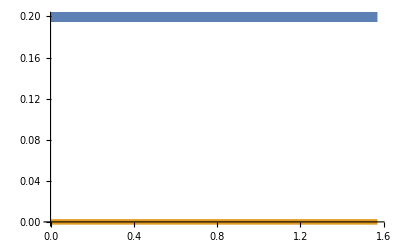

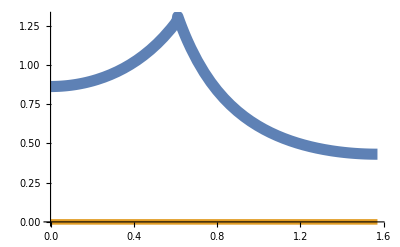

```mathematica
Plot[{fieldRe[x],fieldIm[x]},{x,0,Pi/2},PlotStyle->{{Thickness[0.02]},{Thickness[0.01]}}]
Plot[{DfieldRe[x],DfieldIm[x]},{x,0,Pi/2},PlotStyle->{{Thickness[0.02]},{Thickness[0.01]}}]
```

## Compute the Fourier Spectrum of the Source

```mathematica
mπ=0.14;
GeVtoIfm=5.0677;
fmtoIGeV=GeVtoIfm;

ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

G0[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
G0ANTI[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p]);(*dimensionless*)
G1[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]+I*J1tw[α,p]);(*dimensionless*)
G1ANTI[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]-I*J1tw[α,p]);(*dimensionless*)
```

```mathematica
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{G0ps,G1ps,spectrps},
G0ps[α_]=G0[α,ps];
G1ps[α_]=G1[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ps[α]+f[α]*G1ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
ComputeSourceSpectrAnti[ps_,f_,Df_]:=Module[{G0ANTIps,G1ANTIps,spectrps},
G0ANTIps[α_]=G0ANTI[α,ps];
G1ANTIps[α_]=G1ANTI[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ANTIps[α]+f[α]*G1ANTIps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
```

```mathematica
linspace[a_,b_,N_]:=Range[a,b,(b-a)/N];
ps=N@linspace[0,1,100]
myf[x_]=fieldRe[x]+fieldIm[x];
myDf[x_]=DfieldRe[x]+DfieldIm[x];
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Jspec=ComputeSourceSpectr[ps,myf,myDf];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -383.131+412.345 ⅈ and 0.0101413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -380.946+391.875 ⅈ and 0.00962793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -371.551+333.757 ⅈ and 0.00818288 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
JspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -572.541-252.825 ⅈ and 0.00897597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -561.752-231.534 ⅈ and 0.00853749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -527.481-172.423 ⅈ and 0.00729629 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{# 20241029_112541},{# initdata:	data/init_real_m140_constfield_20241029_110519/R10.csv},{# particle mass:	0.14},{# NpT:	200},{# pTmax:	2},{# epsabs:	0},{# epsrel:	1e-05},{# integr iter:	10000},«193»,{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{# 20241029_112541},{# initdata:	data/init_real_m140_constfield_20241029_110519/R10.csv},{# particle mass:	0.14},{# NpT:	200},{# pTmax:	2},{# epsabs:	0},{# epsrel:	1e-05},{# integr iter:	10000},«193»,{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{0,74762.2,0},{0.0100503,70367.4,0},{0.0201005,58804.3,0},{0.0301508,44017.8,0},{0.040201,30176.6,0},{0.0502513,19807.3,0},{0.0603015,13213.5,0},{0.0703518,9207.78,0},{0.080402,6378.36,0},«182»,{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

{{0,74762.2,0},{0.0100503,70367.4,0},{0.0201005,58804.3,0},{0.0301508,44017.8,0},{0.040201,30176.6,0},{0.0502513,19807.3,0},{0.0603015,13213.5,0},{0.0703518,9207.78,0},{0.080402,6378.36,0},«182»,{1.9196,0.262661,0},{1.92965,0.214646,0},{1.9397,0.10579,0},{1.94975,0.0185408,0},{1.9598,0.00411164,0},{1.96985,0.0579463,0},{1.9799,0.141388,0},{1.98995,0.207496,0},{2,0.215621,0}}

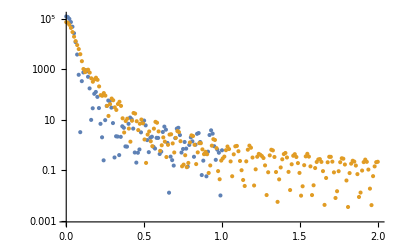

-Graphics-

```mathematica
Short[mycppspeccsv=Import[StringJoin[myspec,"/spectr.txt"],"CSV"],5]
Short[mycppspecanticsv=Import[StringJoin[myspec,"/spectr_anti.txt"],"CSV"],5]

Short[mycppspec=mycppspeccsv[[10;;]],5]
Short[mycppspecanti=mycppspecanticsv[[10;;]],5]

mycppspecPt=(Transpose@mycppspec)[[1]];
mycppspecAntiPt=(Transpose@mycppspec)[[1]];

mycppspecAbs2=(Transpose@mycppspec)[[2]];
mycppspecAntiAbs2=(Transpose@mycppspec)[[2]];

ListLogPlot[{Transpose@{ps,Abs@(Jspec)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
ListLogPlot[{Transpose@{ps,Abs@(JspecAnti)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAntiAbs2}}]
```

```mathematica
T=12.56;
R=8.52;
τ0=0.4;
AT=0.127;
BT=0;
AR=0.127;
BR=0;

J0Rp[p_,R_]:=BesselJ[0,R*p*GeVtoIfm];(*dimensionless*)
J1Rp[p_,R_]:=BesselJ[1,R*p*GeVtoIfm];(*dimensionless*)
Y0Tw[p_,T_]:=BesselY[0,T*ω[p]*GeVtoIfm];(*dimensionless*)
Y1Tw[p_,T_]:=BesselY[1,T*ω[p]*GeVtoIfm];(*dimensionless*)
Y1t0w[p_]:=BesselY[1,τ0*ω[p]*GeVtoIfm];(*dimensionless*)
J0Tw[p_,T_]:=BesselJ[0,T*ω[p]*GeVtoIfm];(*dimensionless*)
J1Tw[p_,T_]:=BesselJ[1,T*ω[p]*GeVtoIfm];(*dimensionless*)
J1t0w[p_]:=BesselJ[1,τ0*ω[p]*GeVtoIfm];(*dimensionless*)

JT[p_,T_,R_,AT_,BT_]:=2*Pi^2*(T*R*fmtoIGeV^2)/p*(BT*(-Y0Tw[p,T]+I*J0Tw[p,T])+AT*ω[p]*(-Y1Tw[p,T]+ⅈ*J1Tw[p,T]))*J1Rp[p,R];
JR[p_,T_,R_,AR_,BR_]:=-2*Pi^2*(R*fmtoIGeV^2)/ω[p]*(BR*J0Rp[p,R]+AR*p*J1Rp[p,R])*(
	T*(-Y1Tw[p,T]+ⅈ*J1Tw[p,T])-τ0*(-Y1t0w[p]+ⅈ*J1t0w[p])
);
Jan[p_,T_,R_,AT_,BT_,AR_,BR_]:=JT[p,T,R,AT,BT]+JR[p,T,R,AR,BR];
```

```mathematica
Off[Power::infy,Infinity::indet]
Manipulate[
ListLogPlot[{
Transpose@{ps,Abs@(Jspec)^2/(2*Pi)^3},
Transpose@{ps,Abs@(Jan[ps,T,R,AT,BT,AR,BR])^2/(2*Pi)^3},
Transpose@{mycppspecPt,mycppspecAbs2}
},
PlotRange->{{0,1},{0.01,1000000}},
PlotLegends->{"numeric, simplified geometry","analytic","numeric, full geometry"}],
{{T,12.56},10,15},
{{R,8.52},7,12},
{{AT,0.1},-0.5,0.5},
{{BT,0},-0.5,0.5},
{{AR,0.1},-0.5,0.5},
{{BR,0},-0.5,0.5}
]
Off[Power::infy,Infinity::indet]
```

```mathematica
JT2[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*NIntegrate[rr*fmtoIGeV*fmtoIGeV*BesselJ[0,rr*p*GeVtoIfm],{rr,0,R},Method->{Automatic,"SymbolicProcessing"->0}];
JR2[p_]:=2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*NIntegrate[tt*fmtoIGeV*fmtoIGeV*(-BesselY[0,tt*ω[p]*GeVtoIfm]+I*BesselJ[0,tt*ω[p]*GeVtoIfm]),{tt,0,T},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
sampleps =linspace[0,1,100];
JT2ps=JT2[sampleps];
JR2ps=JR2[sampleps];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) π π ComplexInfinity encountered.

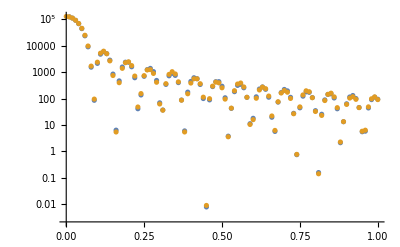

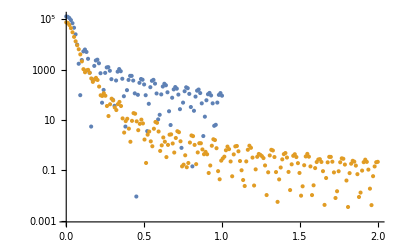

```mathematica
ListLogPlot[{Transpose@{ps,Abs@(JT[ps]+JR[ps])^2/(2*Pi)^3},Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
```

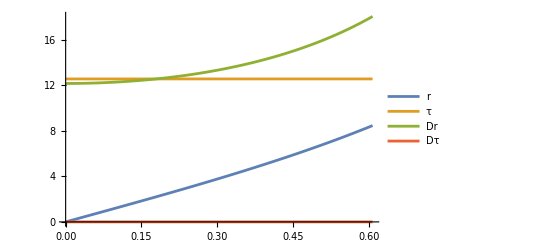

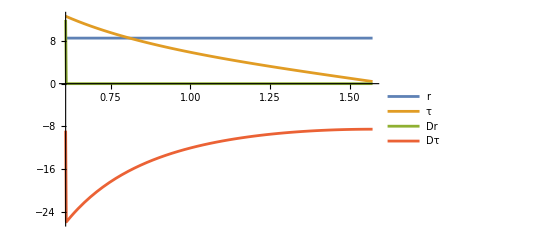

```mathematica
Plot[{r[α],τ[α],Dr[α],Dτ[α]},{α,0,0.60792},PlotLegends->{"r","τ","Dr","Dτ"}]
Plot[{r[α],τ[α],Dr[α],Dτ[α]},{α,0.609,Pi/2},PlotLegends->{"r","τ","Dr","Dτ"}]
```

```mathematica
JT3[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*NIntegrate[r[α]*fmtoIGeV*Dr[α]*fmtoIGeV*BesselJ[0,r[α]*p*GeVtoIfm],{α,0,0.60792},Method->{Automatic,"SymbolicProcessing"->0}];
JR3[p_]:=2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*NIntegrate[τ[α]*fmtoIGeV*Dτ[α]*fmtoIGeV*(-BesselY[0,τ[α]*ω[p]*GeVtoIfm]+I*BesselJ[0,τ[α]*ω[p]*GeVtoIfm]),{α,0.61,Pi/2},Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
sampleps =linspace[0,1,100];
JT3ps=JT3[sampleps];
JR3ps=JR3[sampleps];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.59742981148369055099944802122990950010716915130615234375}. NIntegrate obtained -0.8169 and 6.37022×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.597429811483691}. NIntegrate obtained 3.80381 and 4.70724×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.523609}. NIntegrate obtained 1.91583 and 2.0717×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 74.0846-113.39 ⅈ and 0.00369177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 76.3588-112.036 ⅈ and 0.00369111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.61167957808648846531295040218623171313083730638027191162109375}. NIntegrate obtained 82.9129-107.711 ⅈ and 0.00368918 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) π π ComplexInfinity encountered.

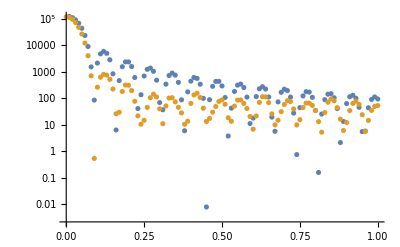

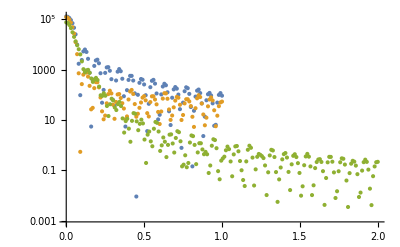

```mathematica
ListLogPlot[{Transpose@{ps,Abs@(JT[ps]+JR[ps])^2/(2*Pi)^3},Transpose@{ps,Abs@(JT3ps+JR3ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{ps,Abs@(JT2ps+JR2ps)^2/(2*Pi)^3},Transpose@{ps,Abs@(JT3ps+JR3ps)^2/(2*Pi)^3},Transpose@{mycppspecPt,mycppspecAbs2}}]
```

```mathematica
J3[p_]:=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*
(A*
(Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]+I*J1tw[α,p]))
),
{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
J3T[p_]:=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*
(A*
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]+I*J1tw[α,p])
),
{α,0,0.608},
Method->{Automatic,"SymbolicProcessing"->0}
];
J3R[p_]:=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*
(A*
Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])
),
{α,0.608,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
J4T[p_]:=2*Pi^2*NIntegrate[
τ[0.608]*rr*fmtoIGeV^2*
(A*
fmtoIGeV*ω[p]*BesselJ[0,rr*p*GeVtoIfm]*(-BesselY[1,τ[0.608]*ω[p]*GeVtoIfm]+I*BesselJ[1,τ[0.608]*ω[p]*GeVtoIfm])
),
{rr,0,r[0.608]},
Method->{Automatic,"SymbolicProcessing"->0}
];
J4R[p_]:=2*Pi^2*NIntegrate[
ττ*r[0.608]*fmtoIGeV^2*
(A*
fmtoIGeV*p*BesselJ[1,r[0.608]*p*GeVtoIfm]*(-BesselY[0,ττ*ω[p]*GeVtoIfm]+I*BesselJ[0,ττ*ω[p]*GeVtoIfm])
),
{ττ,τ[0.608],τ[Pi/2]},
Method->{Automatic,"SymbolicProcessing"->0}
];
J5T[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*NIntegrate[rr*fmtoIGeV*fmtoIGeV*BesselJ[0,rr*p*GeVtoIfm],{rr,0,R},Method->{Automatic,"SymbolicProcessing"->0}];
J5R[p_]:=2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*NIntegrate[tt*fmtoIGeV*fmtoIGeV*(-BesselY[0,tt*ω[p]*GeVtoIfm]+I*BesselJ[0,tt*ω[p]*GeVtoIfm]),{tt,T,τ[Pi/2]},Method->{Automatic,"SymbolicProcessing"->0}];
J6T[p_]:=2*Pi^2*T*fmtoIGeV*A*ω[p]*(-Y1Tw[p]+I*J1Tw[p])*1/p^2 GeVtoIfm*p*R*BesselJ[1,GeVtoIfm*p*R];
J6R[p_]:=-2*Pi^2*R*fmtoIGeV*A*p*J1Rp[p]*1/ω[p]^2*(
GeVtoIfm*ω[p]*T*(-BesselY[1,GeVtoIfm*ω[p]*T]+I*BesselJ[1,GeVtoIfm*ω[p]*T])-
GeVtoIfm*ω[p]*τ[Pi/2]*(-BesselY[1,GeVtoIfm*ω[p]*τ[Pi/2]]+I*BesselJ[1,GeVtoIfm*ω[p]*τ[Pi/2]])
);
```

```mathematica
J3ps=J3[sampleps];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -87.8723+268.595 ⅈ and 0.00531908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -90.9742+259.447 ⅈ and 0.0069619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.613568}. NIntegrate obtained -98.5083+232.833 ⅈ and 0.00462306 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-1734.53+5301.86 ⅈ,-1795.76+5121.29 ⅈ,-1944.48+4595.94 ⅈ,-2088.19+3780.46 ⅈ,-2111.8+2777.97 ⅈ,-1926.42+1739.68 ⅈ,-1515.08+840.038 ⅈ,-953.171+227.178 ⅈ,-387.283-32.8355 ⅈ,25.2371+12.7182 ⅈ,189.265+220.574 ⅈ,117.924+416.412 ⅈ,-77.2694+476.112 ⅈ,-249.259+378.17 ⅈ,-295.052+197.056 ⅈ,-204.245+43.5724 ⅈ,-48.8507-8.15822 ⅈ,74.4177+39.3866 ⅈ,107.997+121.971 ⅈ,61.6451+166.519 ⅈ,-8.43388+141.452 ⅈ,-47.7341+70.3675 ⅈ,-41.0593+5.0392 ⅈ,-14.6394-16.8924 ⅈ,-7.07154+3.3125 ⅈ,-35.6482+33.5668 ⅈ,-84.2051+40.7273 ⅈ,-118.734+16.3915 ⅈ,-115.126-20.2317 ⅈ,-76.2926-41.2456 ⅈ,-27.0281-33.1974 ⅈ,6.58937-5.9885 ⅈ,15.5683+17.5004 ⅈ,10.5243+20.5913 ⅈ,8.70508+4.75969 ⅈ,17.8952-14.175 ⅈ,30.572-20.8134 ⅈ,32.0556-12.8777 ⅈ,14.6529-1.69314 ⅈ,-14.5625-1.05727 ⅈ,-38.7211-14.6331 ⅈ,-44.3075-32.6715 ⅈ,-31.2531-40.5077 ⅈ,-11.6595-31.1663 ⅈ,1.24528-11.0941 ⅈ,4.01736+5.78086 ⅈ,4.31639+10.1565 ⅈ,11.9225+4.78833 ⅈ,28.0376+0.747887 ⅈ,42.9561+6.20192 ⅈ,44.4149+18.2448 ⅈ,28.9572+25.4599 ⅈ,5.67847+18.8568 ⅈ,-11.3087+0.879583 ⅈ,-14.8164-16.1297 ⅈ,-9.8665-20.7412 ⅈ,-7.51571-12.4054 ⅈ,-13.3239-1.1873 ⅈ,-21.6876+2.38875 ⅈ,-21.5823-2.48029 ⅈ,-8.10382-6.56506 ⅈ,11.596-0.439259 ⅈ,24.0508+15.2553 ⅈ,21.5743+29.3754 ⅈ,9.02568+30.393 ⅈ,-1.31928+17.2265 ⅈ,-1.75824+0.28168 ⅈ,3.76475-8.44992 ⅈ,4.43542-6.50434 ⅈ,-5.67287-2.36661 ⅈ,-20.7256-5.9262 ⅈ,-28.2105-17.6266 ⅈ,-21.0611-27.3453 ⅈ,-4.77146-24.2861 ⅈ,7.69203-8.06177 ⅈ,8.22676+10.2024 ⅈ,0.948598+18.0373 ⅈ,-2.70094+13.0618 ⅈ,3.91126+4.38568 ⅈ,15.5458+2.70447 ⅈ,20.2892+9.17532 ⅈ,11.8005+14.3666 ⅈ,-3.81625+8.35266 ⅈ,-13.5905-8.33 ⅈ,-10.2272-24.1292 ⅈ,0.963508-27.1245 ⅈ,7.72077-16.3062 ⅈ,3.32546-2.19773 ⅈ,-6.70905+3.77326 ⅈ,-10.5276+0.39623 ⅈ,-2.37461-2.92064 ⅈ,11.1361+3.24786 ⅈ,17.3997+17.6933 ⅈ,10.4411+28.9091 ⅈ,-3.03068+26.2575 ⅈ,-10.334+10.7088 ⅈ,-5.50775-5.78197 ⅈ,4.87661-11.7248 ⅈ,8.68223-6.84481 ⅈ,0.806687-1.34652 ⅈ,-11.4723-4.60256 ⅈ}

```mathematica
J3Tps=J3T[sampleps];
J3Rps=J3R[sampleps];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.60791624151335330566829368709180769769773178268224000930786132813}. NIntegrate obtained 1.69791+0.762317 ⅈ and 0.0000174118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.60791624151335330566829368709180769769773178268224000930786132813}. NIntegrate obtained 5.9634+4.98933 ⅈ and 0.0000131891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.60791624151335330566829368709180769769773178268224000930786132813}. NIntegrate obtained -4.71897-3.75318 ⅈ and 0.0000103728 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.611784009971268662002319427273278051870875060558319091796875}. NIntegrate obtained 0.904546-1.29762 ⅈ and 0.0000150593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.611784009971268662002319427273278051870875060558319091796875}. NIntegrate obtained 3.65163-4.64215 ⅈ and 0.0000559405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.611784009971268662002319427273278051870875060558319091796875}. NIntegrate obtained 8.12227-8.53517 ⅈ and 0.000110824 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
J4Tps=J4T[sampleps];
J4Rps=J4R[sampleps];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
J5Tps=J5T[sampleps];
J5Rps=J5R[sampleps];
```

```mathematica
J6Tps=J6T[sampleps];
J6Rps=J6R[sampleps];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) π^2 ComplexInfinity encountered.

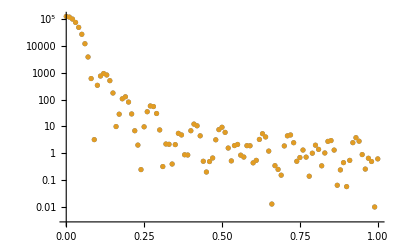

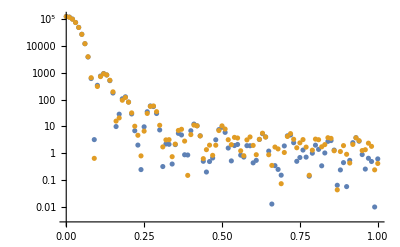

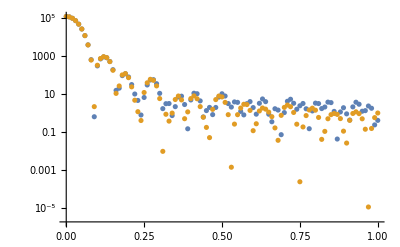

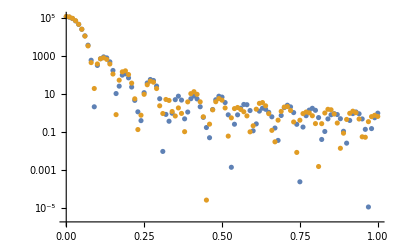

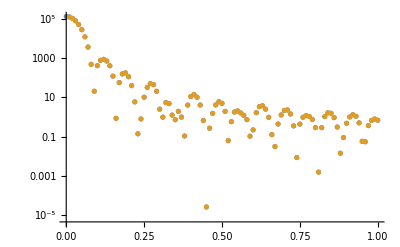

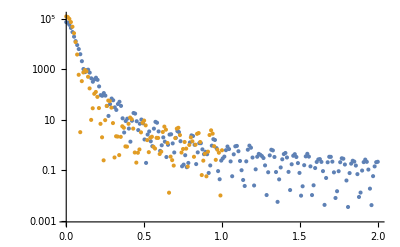

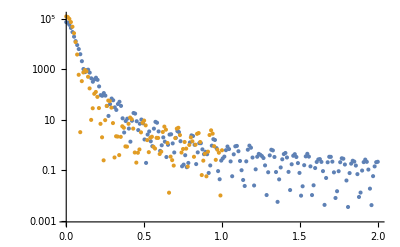

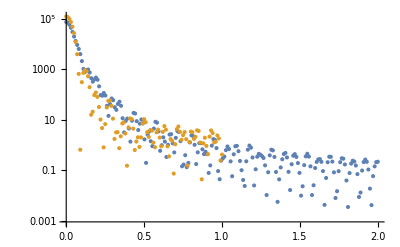

```mathematica
ListLogPlot[{Transpose@{sampleps,Abs@(Jspec)^2/(2*Pi)^3},Transpose@{ps,Abs@(J3ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{sampleps,Abs@(J3ps)^2/(2*Pi)^3},Transpose@{ps,Abs@(J3Rps+J3Tps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{sampleps,Abs@(J3Rps+J3Tps)^2/(2*Pi)^3},Transpose@{ps,Abs@(J4Tps+J4Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{sampleps,Abs@(J4Tps+J4Rps)^2/(2*Pi)^3},Transpose@{ps,Abs@(J5Tps+J5Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{ps,Abs@(J5Tps+J5Rps)^2/(2*Pi)^3},Transpose@{sampleps,Abs@(J6Tps+J6Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(Jspec)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(J3ps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(J3Tps+J3Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(J4Tps+J4Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(J5Tps+J5Rps)^2/(2*Pi)^3}}]
ListLogPlot[{Transpose@{mycppspecPt,mycppspecAbs2},Transpose@{sampleps,Abs@(J6Tps+J6Rps)^2/(2*Pi)^3}}]
```